```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/neerajsarna/sciebo/DG_MPI/plotting_routines

## Importing data

```mathematica
(*observed error, flag == 0,
 error grid, flag == 1 and 
error velocity flag == 2
num sol flag == 3
adjoint sol == 4*)
importdata[cycle_,flag_,outputdir_]:=Module[{result,filename},
Which[flag == 0,
filename=StringJoin["../",outputdir,"/error_observed_cycle",ToString[cycle],".txt"],
flag == 1,
filename=StringJoin["../",outputdir,"/error_grid_cycle",ToString[cycle],".txt"],

flag == 2,
filename=StringJoin["../",outputdir,"/error_velocity_cycle",ToString[cycle],".txt"],
flag == 3,
filename=StringJoin["../",outputdir,"/result_cycle",ToString[cycle],".txt"],
flag == 4,
filename=StringJoin["../",outputdir,"/resultAdj_cycle",ToString[cycle],".txt"],
flag == 5,
filename=StringJoin["../",outputdir,"/fe_index_cycle",ToString[cycle],".txt"]
];

Print[Style["Reading Data from...",FontColor->Black]];
Print[Style[ToString[filename],FontColor->Green]];
result = Import[filename,"Table"]
]

SortData[data_]:=Module[{indices},
indices = Ordering[data⟦All,1⟧,All,GreaterEqual];
data⟦indices,All⟧
]
```

## Code validation

```mathematica
ReturnError[dataMom_,dataDVM_]:=Norm[dataMom⟦All,3⟧-dataDVM⟦All,3⟧];
```

```mathematica
Mvalues = Range[3,13,2];
resultDvm = Import["/Users/neerajsarna/sciebo/StaRMAP_ver1p9/SBP_Traditional/generic_2D/sbp_sat/DVM/result_Comp/result_DVM.txt","Table"];
Do[resultMom[ii]=Import[StringJoin["/Users/neerajsarna/sciebo/StaRMAP_ver1p9/SBP_Traditional/generic_2D/sbp_sat/DVM/result_Comp/result_M",ToString[ii],".txt"],"Table"],{ii,Mvalues}];
```

```mathematica
ListPlot3D[Transpose[resultDvm⟦{1,2,10},All⟧],PlotRange->Full,ColorFunction->"Rainbow",PlotLegends->Automatic]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose[resultMom[13]⟦{1,2,10},All⟧],PlotRange->Full,ColorFunction->"Rainbow",PlotLegends->Automatic]
```

-Graphics3D-

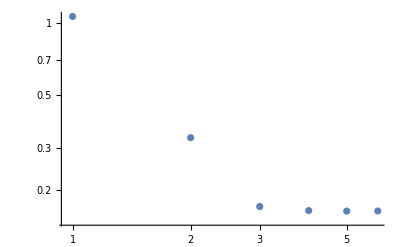

```mathematica
variable = 9;
error=Table[ReturnError[Transpose[resultDvm⟦{1,2,variable},All⟧],Transpose[resultMom[ii]⟦{1,2,variable},All⟧]],{ii,Mvalues}];
ListLogLogPlot[error]
```

```mathematica
Length[Transpose[resultDvm⟦{1,2,11},All⟧]⟦All,3⟧]
```

6561

```mathematica
Length[Transpose[resultMom[9]⟦{1,2,11},All⟧]⟦All,3⟧]
```

10201